Autor: JOE MAMA

# Metody numeryczne (Informatyka)

## Projekt 2

Metoda Newtona

Napisać procedurę realizującą algorytm metody stycznych (Newtona) (argumenty:  f, x_0,  e).
Napisać także procedurę realizującą algorytm metody Newtona dla układu dwóch równań nieliniowych (argumenty:  f, g, v_0,  e).

Korzystając z napisanych procedur:

a) Wyznaczyć pierwiastek 6 stopnia ze 101 z dokładnością 10^-10.

b) W pewnym układzie elektrycznym z diodą tunelową natężenie prądu i oraz napięcie u spełniają układ równań:

i=k u (u^2/3-3/2 u+2),
u/r+i=j,

gdzie k=1 mA/V^3, j=1 mA, r= 10 kΩ. Wykorzystując metodę Newtona wyznaczyć natężenie prądu oraz napięcie. Rozwiązanie zilustrować graficznie (można do tego celu wykorzystać instrukcję ContourPlot).

## Rozwiązanie

### Program (jedno równanie)

```mathematica
newton1[f_,x0_,e_] := Module[{xs,xn},
xs = x0+2e; xn = x0;
While[Abs[f[xn]]>e,
xs = xn;
xn = xs - f[xs]/f'[xs];
];
Return[xn]
]
```

### Przykład testowy (jedno równanie)

```mathematica
Clear[f];
f[x_]:=x^2-3;

newton1[f,3., 0.01]
```

1.73214

### Program (układ dwóch równań)

```mathematica
wsk3[f_,g_,a_,b_]:=Module[{c,j,c1},
(* Symboliczne wyznaczenie macierzy Jacobiego *)
j= {{D[f[x,y],x],D[f[x,y],y]}, {D[g[x,y],x], D[g[x,y],y]}};
(* macierz Jacobiego w punkcie (a,b) *)
c=j/.{x->a, y->b};
(* macierz odwrotna *)
c1 = Inverse[c];
Return[c1]]
```

```mathematica
newton2[f1_,f2_,x0_,e_] := Module[{xs,xn,p},
xs=x0+2e;xn=x0;
While[Norm[f1[xs[[1]],xs[[2]]],f2[xs[[1]],xs[[2]]]]<e,
xs =xn;
p=wsk3[f1,f2,xs[[1]],xs[[2]]];
xn=xs-p.{f1[xs[[1]],xs[[2]]],f2[xs[[1]],xs[[2]]]};
];
Return[N[xn]]
]
```

### Zadanie a)

```mathematica
g[x_]=x^6-101;
```

```mathematica
NumberForm[newton1[g,150.,10^-10], 11]
```

2.158010544

### Zadanie b)

```mathematica
Clear[k,j,r,i,g];
```

{5.,5.}

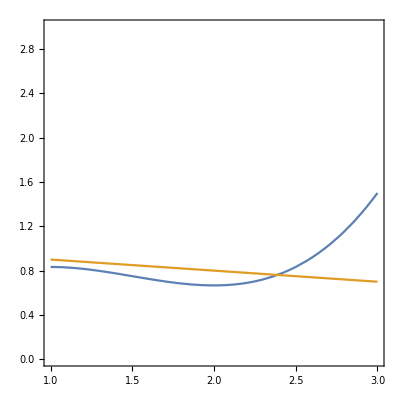

```mathematica
k=1;
j=1;
r=10;
fi[u_,i_]:=k*u*(u^2/3-3/2*u+2)-i;
fg[u_,i_]:=u/r+i-j;
newton2[fi, fg,{5,5},0.01]
ContourPlot[{fi[x,y], fg[x,y]},{x,1,3},{y,0,3}]
```